# Метод на разполовяването

Задача 1: Дадено е уравенението:
(a-9 x)/(x^2+b+1) - x^2+ (2a + 1)sinx + a + b = 0, където а е предпоследната цифра на факултетния ни
номер, а b последната.
=>  (0-9 x)/(x^2+9)- x^2+ sinx + 8 = 0;
1. Представете геометрична интерпретация на уравнението.
2. Да се локализира един от корените.
3. Уточнете локализирания корен по метода на разполовяването.
4. Оценка на грешката.
5. Колко биха били броя на итерациите за достигане на точност 0.0001 по метода на разполовяването, използвайки интервала от локализацията на корена.

```mathematica
f[x_]:=(0-9x)/(x^2+9)-x^2+Sin[x]+8
```

```mathematica
f[x]
```

8-x^2-(9 x)/(9+x^2)+Sin[x]

## 1.Визуализация на функцията

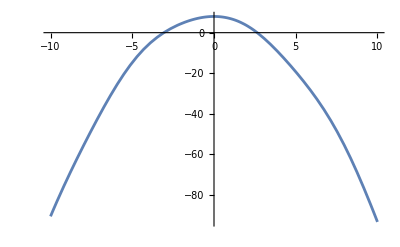

```mathematica
Plot[f[x],{x,-10,10}]
```

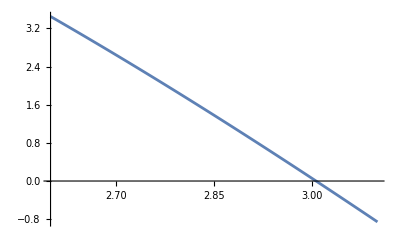

```mathematica
Plot[f[x],{x,2.6,3.1}]
```

## 3. Уточнете локализирания корен по метода на разполовяването.

```mathematica
f[x_]:=(0-9x)/(x^2+9)-x^2+Sin[x]+8
```

```mathematica
a=2.6;b=3.1;
For[n=0,n<6,n++,
Print["n= ",n," a_n= ",a," b_n= ",b," m_n= ",m=(a+b)/2," f(m_n)= ",f[m]," ϵ_n= ",(b-a)/2];
If[f[m]>0,a=m,b=m]
]
```

n= 0 a_n= 2.6 b_n= 3.1 m_n= 2.85 f(m_n)= -1.33305 ϵ_n= 0.25

n= 1 a_n= 2.6 b_n= 2.85 m_n= 2.725 f(m_n)= -0.514072 ϵ_n= 0.125

n= 2 a_n= 2.6 b_n= 2.725 m_n= 2.6625 f(m_n)= -0.117312 ϵ_n= 0.0625

n= 3 a_n= 2.6 b_n= 2.6625 m_n= 2.63125 f(m_n)= 0.0778088 ϵ_n= 0.03125

n= 4 a_n= 2.63125 b_n= 2.6625 m_n= 2.64688 f(m_n)= -0.0194781 ϵ_n= 0.015625

n= 5 a_n= 2.63125 b_n= 2.64688 m_n= 2.63906 f(m_n)= 0.0292339 ϵ_n= 0.0078125

## 4.Оценка на грешката

```mathematica
f[x_]:=(0-9x)/(x^2+9)-x^2+Sin[x]+8
```

```mathematica
a=2.6;b=3.1;
epszad=0.00001;
eps=Infinity;
For[n=0,eps>epszad,n++,
Print["n= ",n," a_n= ",a," b_n= ",b," m_n= ",m=(a+b)/2," f(m_n)= ",f[m]," ϵ_n= ",eps=(b-a)/2];
If[f[m]>0,a=m,b=m]
]
```

n= 0 a_n= 2.6 b_n= 3.1 m_n= 2.85 f(m_n)= -1.33305 ϵ_n= 0.25

n= 1 a_n= 2.6 b_n= 2.85 m_n= 2.725 f(m_n)= -0.514072 ϵ_n= 0.125

n= 2 a_n= 2.6 b_n= 2.725 m_n= 2.6625 f(m_n)= -0.117312 ϵ_n= 0.0625

n= 3 a_n= 2.6 b_n= 2.6625 m_n= 2.63125 f(m_n)= 0.0778088 ϵ_n= 0.03125

n= 4 a_n= 2.63125 b_n= 2.6625 m_n= 2.64688 f(m_n)= -0.0194781 ϵ_n= 0.015625

n= 5 a_n= 2.63125 b_n= 2.64688 m_n= 2.63906 f(m_n)= 0.0292339 ϵ_n= 0.0078125

n= 6 a_n= 2.63906 b_n= 2.64688 m_n= 2.64297 f(m_n)= 0.00489507 ϵ_n= 0.00390625

n= 7 a_n= 2.64297 b_n= 2.64688 m_n= 2.64492 f(m_n)= -0.00728722 ϵ_n= 0.00195313

n= 8 a_n= 2.64297 b_n= 2.64492 m_n= 2.64395 f(m_n)= -0.001195 ϵ_n= 0.000976563

n= 9 a_n= 2.64297 b_n= 2.64395 m_n= 2.64346 f(m_n)= 0.0018503 ϵ_n= 0.000488281

n= 10 a_n= 2.64346 b_n= 2.64395 m_n= 2.6437 f(m_n)= 0.000327716 ϵ_n= 0.000244141

n= 11 a_n= 2.6437 b_n= 2.64395 m_n= 2.64382 f(m_n)= -0.000433627 ϵ_n= 0.00012207

n= 12 a_n= 2.6437 b_n= 2.64382 m_n= 2.64376 f(m_n)= -0.0000529511 ϵ_n= 0.0000610352

n= 13 a_n= 2.6437 b_n= 2.64376 m_n= 2.64373 f(m_n)= 0.000137384 ϵ_n= 0.0000305176

n= 14 a_n= 2.64373 b_n= 2.64376 m_n= 2.64375 f(m_n)= 0.0000422165 ϵ_n= 0.0000152588

n= 15 a_n= 2.64375 b_n= 2.64376 m_n= 2.64375 f(m_n)= -5.36726×10^-6 ϵ_n= 7.62939×10^-6

Колко биха били броя на итерациите за достигане на точност 0.0000001 по метода на разполовяването,използвайки интервала от локализацията на корена.

```mathematica
Log2[(3.1-2.6)/0.0000001]-1
```

21.2535

Извод: Нужни са 21 итерации за да се достигне съответната точност.